```mathematica
Quit[]
```

```mathematica
ready
```

ready

```mathematica
SetDirectory[NotebookDirectory[]];
```

# General case numerical calculation

## Factors and definitions

```mathematica
y=1-1/(2v^2);
```

```mathematica
facI=2^(1+2b)*Pi*(2+b)/(3+2b)*Gamma[b+3/2]^2*(v*v)^(-b-1/2)//PowerExpand//FullSimplify;
facI2=xrh^(-2-2*b)*2^(1+4b)*(2+b)^2/(3+2b)^2*Gamma[b+3/2]^4*(v*v)^(-2)*(1-y^2)^b//FullSimplify;
```

```mathematica
P[m_,n_,x_]=((1+x)/(1-x))^(m/2)*1/Gamma[1-m]*Hypergeometric2F1[n+1,-n,1-m,1/2(1-x)];
```

```mathematica
Q[m_,n_,x_]=Pi/2/Sin[Pi*m]*(Cos[Pi*m]*((1+x)/(1-x))^(m/2)*1/Gamma[1-m]*Hypergeometric2F1[n+1,-n,1-m,1/2(1-x)]-Gamma[n+m+1]/Gamma[n-m+1]*((1-x)/(1+x))^(m/2)*1/Gamma[1+m]*Hypergeometric2F1[n+1,-n,1+m,1/2(1-x)]);
```

## Exact formulas

```mathematica
P1w0[y_]=1/2 √(1-x) √(1+x)/.x->y;
P2w0[y_]=1/8 √(1-x) √(1+x) (-1+5 x^2)/.x->y;Q1w0[y_]=(2 x-(-1+x^2) Log[(1+x)/(1-x)])/(4 √(1-x^2))/.x->y;Q2w0[y_]=(-26 x+30 x^3-3 (1-6 x^2+5 x^4) Log[(1+x)/(1-x)])/(48 √(1-x^2))/.x->y;
```

```mathematica
P1wm19[y_]=-1/8 (-1+x) (1+x)/.x->y;P2wm19[y_]=-1/48 (-1+x) (1+x) (-1+7 x^2)/.x->y;Q1wm19[y_]=(x (-5+3 x^2))/(24 (-1+x^2))-1/16 (-1+x^2) Log[(1+x)/(1-x)]/.x->y;Q2wm19[y_]=(x (81-190 x^2+105 x^4))/(720 (-1+x^2))-1/96 (1-8 x^2+7 x^4) Log[(1+x)/(1-x)]/.x->y;
```

```mathematica
P1wm115[y_]=1/3 √(2/π) (1-x)^(3/4) (1+x)^(3/4)/.x->y;P2wm115[y_]=1/15 √(2/π) (1-x)^(3/4) (1+x)^(3/4) (-1+6 x^2)/.x->y;Q1wm115[y_]=-(√(π/2) x (-3+2 x^2))/(6 (1-x)^(3/4) (1+x)^(3/4))/.x->y;Q2wm115[y_]=-(√(π/2) x (15-40 x^2+24 x^4))/(60 (1-x)^(3/4) (1+x)^(3/4))/.x->y;
```

```mathematica
P1w13[y_]=1/.x->y;P2w13[y_]=1/2 (-1+3 x^2)/.x->y;Q1w13[y_]=1/2 Log[(1+x)/(1-x)]/.x->y;Q2w13[y_]=1/4 (-6 x+(-1+3 x^2) Log[(1+x)/(1-x)])/.x->y;
```

```mathematica
P1w19[y_]=√(2/π) (1-x)^(1/4) (1+x)^(1/4)/.x->y;P2w19[y_]=1/3 √(2/π) (1-x)^(1/4) (1+x)^(1/4) (-1+4 x^2)/.x->y;Q1w19[y_]=(√(π/2) x)/((1-x)^(1/4) (1+x)^(1/4))/.x->y;Q2w19[y_]=(√(π/2) x (-3+4 x^2))/(3 (1-x)^(1/4) (1+x)^(1/4))/.x->y;
```

```mathematica
P1w1[y_]=(√(2/π))/((1-x)^(1/4) (1+x)^(1/4))/.x->y;P2w1[y_]=(√(2/π) (-1+2 x^2))/((1-x)^(1/4) (1+x)^(1/4))/.x->y;Q1w1[y_]=0/.x->y;Q2w1[y_]=-√(2 π) (1-x)^(1/4) x (1+x)^(1/4)/.x->y;
```

## Kernels subh

```mathematica
C1RDsb=1/(1+b)(xrh)^(-1/2-b) (xrh (C1b BesselJ[1/2+b,xrh]+C2b BesselY[1/2+b,xrh]) Cos[xrh/(1+b)]-((1+b) C1b BesselJ[1/2+b,xrh]+(1+b) C2b BesselY[1/2+b,xrh]-xrh (C1b BesselJ[3/2+b,xrh]+C2b*BesselY[3/2+b,xrh])) Sin[xrh/(1+b)])/.xrh->(1+b)k*ksrh;
```

```mathematica
C2RDsb=1/(1+b)(xrh)^(-1/2-b) (((1+b) C1b BesselJ[1/2+b,xrh]+(1+b) C2b BesselY[1/2+b,xrh]-xrh (C1b BesselJ[3/2+b,xrh]+C2b BesselY[3/2+b,xrh])) Cos[xrh/(1+b)]+xrh (C1b BesselJ[1/2+b,xrh]+C2b*BesselY[1/2+b,xrh]) Sin[xrh/(1+b)])/.xrh->(1+b)k*ksrh;
```

```mathematica
C1bsb=-facI*(-4*(v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(3/2)*(Q[-b,b,y]+(2+b)/(1+b)*Q[-b,b+2,y]));
C2bsb=facI*((v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(1/2)*(P[-b,b,y]+(2+b)/(1+b)*P[-b,b+2,y]));
```

```mathematica
C1bsbm12=-facI*(-4*(v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(3/2)*(Q1w1[y]+(2+b)/(1+b)*Q2w1[y]));
C2bsbm12=facI*((v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(1/2)*(P1w1[y]+(2+b)/(1+b)*P2w1[y]));
```

```mathematica
C1bsb0=-facI*(-4*(v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(3/2)*(Q1w13[y]+(2+b)/(1+b)*Q2w13[y]));
C2bsb0=facI*((v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(1/2)*(P1w13[y]+(2+b)/(1+b)*P2w13[y]));
```

```mathematica
C1bsb12=-facI*(-4*(v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(3/2)*(Q1w19[y]+(2+b)/(1+b)*Q2w19[y]));
C2bsb12=facI*((v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(1/2)*(P1w19[y]+(2+b)/(1+b)*P2w19[y]));
```

```mathematica
C1bsb1=-facI*(-4*(v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(3/2)*(Q1w0[y]+(2+b)/(1+b)*Q2w0[y]));
C2bsb1=facI*((v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(1/2)*(P1w0[y]+(2+b)/(1+b)*P2w0[y]));
```

```mathematica
C1bsb32=-facI*(-4*(v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(3/2)*(Q1wm115[y]+(2+b)/(1+b)*Q2wm115[y]));
C2bsb32=facI*((v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(1/2)*(P1wm115[y]+(2+b)/(1+b)*P2wm115[y]));
```

```mathematica
C1bsb2=-facI*(-4*(v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(3/2)*(Q1wm19[y]+(2+b)/(1+b)*Q2wm19[y]));
C2bsb2=facI*((v*v)^(b-1/2)*(1-y^2)^(b/2)/(2Pi)^(1/2)*(P1wm19[y]+(2+b)/(1+b)*P2wm19[y]));
```

```mathematica
I2b=1/2(C1RDsb^2+C2RDsb^2)/.C1b->C1bsb/.C2b->C2bsb;
```

```mathematica
I2bm12=1/2(C1RDsb^2+C2RDsb^2)/.C1b->C1bsbm12/.C2b->C2bsbm12;/.b->-1/2;
```

```mathematica
I2b0=1/2(C1RDsb^2+C2RDsb^2)/.C1b->C1bsb0/.C2b->C2bsb0;/.b->0;
```

```mathematica
I2b12=1/2(C1RDsb^2+C2RDsb^2)/.C1b->C1bsb12/.C2b->C2bsb12;/.b->1/2;
```

```mathematica
I2b1=1/2(C1RDsb^2+C2RDsb^2)/.C1b->C1bsb1/.C2b->C2bsb1;/.b->1;
```

```mathematica
I2b32=1/2(C1RDsb^2+C2RDsb^2)/.C1b->C1bsb32/.C2b->C2bsb32;/.b->3/2;
```

```mathematica
I2b2=1/2(C1RDsb^2+C2RDsb^2)/.C1b->C1bsb2/.C2b->C2bsb2;/.b->2;
```

```mathematica
I2be=facI2*((P[-b,b,y]+(2+b)/(1+b)*P[-b,b+2,y])^2+4/Pi^2(Q[-b,b,y]+(2+b)/(1+b)*Q[-b,b+2,y])^2);
```

```mathematica
I2bm12e=facI2*((P1w1[y]+(2+b)/(1+b)*P2w1[y])^2+4/Pi^2(Q1w1[y]+(2+b)/(1+b)*Q2w1[y])^2)/.b->-1/2;
```

```mathematica
I2b0e=facI2*((P1w13[y]+(2+b)/(1+b)*P2w13[y])^2+4/Pi^2(Q1w13[y]+(2+b)/(1+b)*Q2w13[y])^2)/.b->0;
```

```mathematica
I2b12e=facI2*((P1w19[y]+(2+b)/(1+b)*P2w19[y])^2+4/Pi^2(Q1w19[y]+(2+b)/(1+b)*Q2w19[y])^2)/.b->1/2;
```

```mathematica
I2b1e=facI2*((P1w0[y]+(2+b)/(1+b)*P2w0[y])^2+4/Pi^2(Q1w0[y]+(2+b)/(1+b)*Q2w0[y])^2)/.b->1;
```

```mathematica
I2b32e=facI2*((P1wm115[y]+(2+b)/(1+b)*P2wm115[y])^2+4/Pi^2(Q1wm115[y]+(2+b)/(1+b)*Q2wm115[y])^2)/.b->3/2;
```

```mathematica
I2b2e=facI2*((P1wm19[y]+(2+b)/(1+b)*P2wm19[y])^2+4/Pi^2(Q1wm19[y]+(2+b)/(1+b)*Q2wm19[y])^2)/.b->2;
```

## Kernel superh

```mathematica
C1RDe=C1b+((1-b) C2b xrh^(-2 b))/(1+b);
```

```mathematica
C2RDe=(2 b C2b xrh^(1-2 b))/(1+b)^2;
```

```mathematica
C1RDsp=1/(1+b)(xrh)^(-2 b) (xrh (C2b+C1b (xrh)^(2 b)) Cos[xrh/(1+b)]+((-1+b) C2b-(1+b) C1b (xrh)^(2 b)) Sin[xrh/(1+b)])/.xrh->(1+b)k*ksrh;
```

```mathematica
C2RDsp=1/(1+b)(xrh)^(-2 b) (xrh (C2b+C1b (xrh)^(2 b)) Sin[xrh/(1+b)]+(C2b-b C2b+(1+b) C1b (xrh)^(2 b)) Cos[xrh/(1+b)])/.xrh->(1+b)k*ksrh;
```

```mathematica
C1RDg=1/(1+b)xrh^(-1/2-3 b) (xrh ((C1B2+C1B1 xrh^(2 b)) BesselJ[1/2+b,xrh]+C2B xrh^(1+2 b) BesselY[1/2+b,xrh]) Cos[xrh/(1+b)]+(((-1+b) C1B2-(1+b) C1B1 xrh^(2 b)) BesselJ[1/2+b,xrh]+xrh ((C1B2+C1B1 xrh^(2 b)) BesselJ[3/2+b,xrh]+C2B xrh^(2 b) (-(2+b) BesselY[1/2+b,xrh]+xrh BesselY[3/2+b,xrh]))) Sin[xrh/(1+b)])/.xrh->(1+b)k*ksrh;
```

```mathematica
C2RDg=1/(1+b)xrh^(-1/2-3 b) (((C1B2-b C1B2+(1+b) C1B1 xrh^(2 b)) BesselJ[1/2+b,xrh]+xrh (-(C1B2+C1B1 xrh^(2 b)) BesselJ[3/2+b,xrh]+C2B xrh^(2 b) ((2+b) BesselY[1/2+b,xrh]-xrh BesselY[3/2+b,xrh]))) Cos[xrh/(1+b)]+xrh ((C1B2+C1B1 xrh^(2 b)) BesselJ[1/2+b,xrh]+C2B xrh^(1+2 b) BesselY[1/2+b,xrh]) Sin[xrh/(1+b)])/.xrh->(1+b)k*ksrh;
```

```mathematica
IJ=facI*(2^(-1/2-b) (3+2 b))/((1+b) π Gamma[3/2+b])1/v;
```

```mathematica
IY1=facI*(2^(-3/2-b) (3+2 b) (-((1+b+b^2) π)/Gamma[3/2+b]))/(b (1+b)^2 π^2)v^(2b-1);IY2=facI*(2^(-3/2-b) (3+2 b) (2^(1+2 b) (1+b)  Gamma[1/2+b]))/(b (1+b)^2 π^2)1/v;
```

```mathematica
C1bg2=facI*2^(-b-3/2)/Pi/b/(1+b)*2^(2b+3)*Gamma[b+5/2]/Pi/(1+2b)*1/v;C1bg1=-facI*2^(-b-3/2)*v^(2b-1)/Pi/b/(1+b)*(3+2b)/(1+b)(1+b+b^2)/Gamma[b+3/2];C2bg=facI*(2^(-1/2-b) (3+2 b))/((1+b) π Gamma[3/2+b])1/v;
```

```mathematica
I2bshe=1/2*(C1RDe^2)/.C1b->(2+b)(1+b+b^2)/2/b/(1+b)^2*k^2/.C2b->-2^(1+2b)*(2+b)/b/(1+b)/Pi*Gamma[b+3/2]^2*k^(2+2b);
```

```mathematica
I2bsh=1/2*(C1RDsp^2+C2RDsp^2)/.C1b->(2+b)(1+b+b^2)/2/b/(1+b)^2*k^2/.C2b->-2^(1+2b)*(2+b)/b/(1+b)/Pi*Gamma[b+3/2]^2*k^(2+2b);
```

```mathematica
I2bg=1/2*(C1RDg^2+C2RDg^2)/.C1B1->-IY1/.C1B2->-IY2/.C2B->C2bg;
```

## OMEGASubh

```mathematica
OMGWwb[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2b/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh;
```

```mathematica
OMGWwbm12[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2bm12/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->-1/2;
```

```mathematica
OMGWwb0[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2b0/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->0;
```

```mathematica
OMGWwb12[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2b12/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->1/2;
```

```mathematica
OMGWwb1[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2b1/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->1;
```

```mathematica
OMGWwb32[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2b32/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->3/2;
```

```mathematica
OMGWwb2[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2b2/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->2;
```

```mathematica
OMGWwbe[k_,b_,ksrh_]=(xrh/(1+b))^2/48*8*(1-1/4/v^2)^2*v^2*I2be/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh;
```

```mathematica
OMGWwbm12e[k_,b_,ksrh_]=(xrh/(1+b))^2/48*8*(1-1/4/v^2)^2*v^2*I2bm12e/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->-1/2;
```

```mathematica
OMGWwb0e[k_,b_,ksrh_]=(xrh/(1+b))^2/48*8*(1-1/4/v^2)^2*v^2*I2b0e/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->0;
```

```mathematica
OMGWwb12e[k_,b_,ksrh_]=(xrh/(1+b))^2/48*8*(1-1/4/v^2)^2*v^2*I2b12e/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->1/2;
```

```mathematica
OMGWwb1e[k_,b_,ksrh_]=(xrh/(1+b))^2/48*8*(1-1/4/v^2)^2*v^2*I2b1e/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->1;
```

```mathematica
OMGWwb32e[k_,b_,ksrh_]=(xrh/(1+b))^2/48*8*(1-1/4/v^2)^2*v^2*I2b32e/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->3/2;
```

```mathematica
OMGWwb2e[k_,b_,ksrh_]=(xrh/(1+b))^2/48*8*(1-1/4/v^2)^2*v^2*I2b2e/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh/.b->2;
```

## OMEGASuperhh

```mathematica
OMGWwbsh[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2bsh/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh;
OMGWwbshe[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2bshe/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh;
OMGWwbshg[k_,b_,ksrh_]=1/48*8*(1-1/4/v^2)^2*v^2*I2bg/ksrh^(-2b)/.v->1/k/.xrh->(1+b)k*ksrh;
```

```mathematica
OMGWwbshe[k,b,ksrh]*ksrh^(-2b)
```

((1-k^2/4)^2 (((2+b) (1+b+b^2) k^2)/(2 b (1+b)^2)-(2^(1+2 b) (1-b) (2+b) k^(2+2 b) ((1+b) k ksrh)^(-2 b) Gamma[3/2+b]^2)/(b (1+b)^2 π))^2)/(12 k^2)

```mathematica
((((2+b) (1+b+b^2) k^2)/(2 b (1+b)^2)-(2^(1+2 b) (1-b) (2+b) k^(2+2 b) ((1+b) k ksrh)^(-2 b) Gamma[3/2+b]^2)/(b (1+b)^2 π))^2)/(12 k^2)/.k->k/ks/.ksrh->ks/krh
```

(ks^2 (((2+b) (1+b+b^2) k^2)/(2 b (1+b)^2 ks^2)-(2^(1+2 b) (1-b) (2+b) (((1+b) k)/krh)^(-2 b) (k/ks)^(2+2 b) Gamma[3/2+b]^2)/(b (1+b)^2 π))^2)/(12 k^2)

```mathematica
((((2+b) (1+b+b^2) k^2)/(2 b (1+b)^2))^2)/(12 k^2)/.k->k/ks/.ksrh->ks/krh//FullSimplify
```

((2+b)^2 (1+b+b^2)^2 k^2)/(48 b^2 (1+b)^4 ks^2)

```mathematica
((-(2^(1+2 b) (1-b) (2+b) k^(2+2 b) ((1+b) k ksrh)^(-2 b) Gamma[3/2+b]^2)/(b (1+b)^2 π))^2)/(12 k^2)//PowerExpand//FullSimplify
```

(16^b (1+b)^(-4 (1+b)) (-2+b+b^2)^2 k^2 ksrh^(-4 b) Gamma[3/2+b]^4)/(3 b^2 π^2)

```mathematica
2^4
```

16

```mathematica
(1-b) ^2(2+b) ^2//FullSimplify
```

(-2+b+b^2)^2

# Plotting all

```mathematica
bb[w_]=(1-3w)/(1+3w)
```

(1-3 w)/(1+3 w)

```mathematica
bb[-1/9]
```

2

```mathematica
bb[-1/15]
```

3/2

```mathematica
f[σ_,k_]=Erf[1/σ*ArcSinh[k/2*Exp[σ^2]]]-Erf[1/σ*Re[ArcCosh[k/2*Exp[σ^2]]]];
```

## Plots 1

```mathematica
ksrh=10^2;b=1;k1=1/ksrh/(1+b);
ymax=Log10[OMGWwb1[1/ksrh,b,ksrh]]//N;
ymin=Log10[OMGWwbsh[k1,b,ksrh]]//N;
slope=A/.Flatten[Solve[{ymax==A*Log10[1/ksrh]+B,ymin==A*Log10[k1]+B},{A,B}]];
cnt=B/.Flatten[Solve[{ymax==A*Log10[1/ksrh]+B,ymin==A*Log10[k1]+B},{A,B}]];
```

```mathematica
OMGWwb1[k1,b,ksrh]/OMGWwbshe[k1,b,ksrh]//N
```

0.861359

```mathematica
DOMGWwb1[k_]=D[OMGWwb1[k,b,ksrh],k];
```

```mathematica
DOMGWwbshe[k_]=D[OMGWwbshe[k,b,ksrh],k];
```

```mathematica
k2=k/.FindRoot[DOMGWwb1[k]==DOMGWwbshe[k],{k,0.01}]
```

0.000364474

```mathematica
OMGWwb1[k2,b,ksrh]/OMGWwbshe[k2,b,ksrh]//N
```

1.00242

```mathematica
rangekk1=10^Range[-5,Log10[k2],0.001];rangekk2=10^Range[Log10[k2],Log10[2],0.001];
```

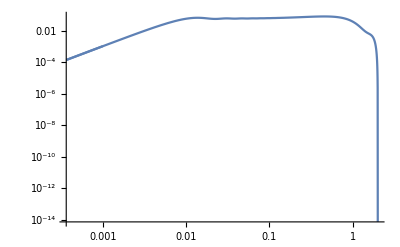

```mathematica
Show[LogLogPlot[{OMGWwb1[k,b,ksrh]},{k,k2,2},PlotRange->All],LogLogPlot[{OMGWwbshe[k,b,ksrh]},{k,10^(-3),k2},PlotRange->All]]
```

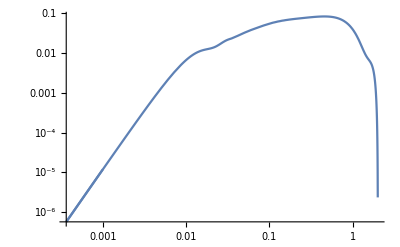

```mathematica
Show[LogLogPlot[{f[0.05,k]*OMGWwb1[k,b,ksrh]},{k,k2,2},PlotRange->All],LogLogPlot[{f[0.05,k]*OMGWwbshe[k,b,ksrh]},{k,10^(-3),k2},PlotRange->All]]
```

```mathematica
L1=Length[rangekk1];L2=Length[rangekk2];
```

```mathematica
OMGWb11=Table[{Log10[rangekk1[[i]]],Log10[f[0.01,rangekk1[[i]]]*OMGWwbshe[rangekk1[[i]],b,ksrh]]},{i,1,L1}];OMGWb12=Table[{Log10[rangekk2[[i]]],Log10[f[0.01,rangekk2[[i]]]*OMGWwb1[rangekk2[[i]],b,ksrh]]},{i,1,L2}];
```

```mathematica
rangekk=Join[rangekk1,rangekk2];
OMGWb1=Join[OMGWb11[[All,2]],OMGWb12[[All,2]]];
```

```mathematica
L=Length[rangekk];
```

```mathematica
OMGWb1list=Table[{Log10[rangekk[[i]]],OMGWb1[[i]]},{i,1,L}];
```

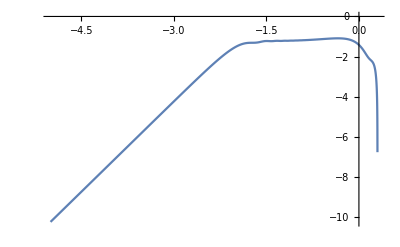

```mathematica
ListLinePlot[OMGWb1list]
```

```mathematica
Export["data/OMGWb1_001.dat",OMGWb1list];
```

```mathematica
L1=Length[rangekk1];L2=Length[rangekk2];
```

```mathematica
OMGWb11=Table[{Log10[rangekk1[[i]]],Log10[f[0.05,rangekk1[[i]]]*OMGWwbshe[rangekk1[[i]],b,ksrh]]},{i,1,L1}];OMGWb12=Table[{Log10[rangekk2[[i]]],Log10[f[0.05,rangekk2[[i]]]*OMGWwb1[rangekk2[[i]],b,ksrh]]},{i,1,L2}];
```

```mathematica
rangekk=Join[rangekk1,rangekk2];
OMGWb1=Join[OMGWb11[[All,2]],OMGWb12[[All,2]]];
```

```mathematica
L=Length[rangekk];
```

```mathematica
OMGWb1list=Table[{Log10[rangekk[[i]]],OMGWb1[[i]]},{i,1,L}];
```

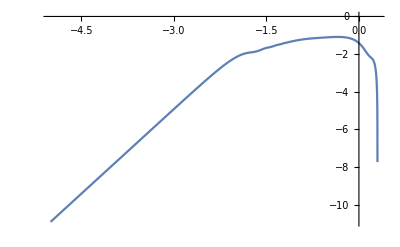

```mathematica
ListLinePlot[OMGWb1list]
```

```mathematica
Export["data/OMGWb1_005.dat",OMGWb1list];
```

## Plots 2

```mathematica
ksrh=10^2;b=3/2;k1=1/ksrh/(1+b);
ymax=Log10[OMGWwb32[1/ksrh,b,ksrh]]//N;
ymin=Log10[OMGWwbsh[k1,b,ksrh]]//N;
slope=A/.Flatten[Solve[{ymax==A*Log10[1/ksrh]+B,ymin==A*Log10[k1]+B},{A,B}]];
cnt=B/.Flatten[Solve[{ymax==A*Log10[1/ksrh]+B,ymin==A*Log10[k1]+B},{A,B}]];
```

```mathematica
OMGWwb32[k1,b,ksrh]/OMGWwbshe[k1,b,ksrh]//N
```

0.869067

```mathematica
DOMGWwb32[k_]=D[OMGWwb32[k,b,ksrh],k];
```

```mathematica
DOMGWwbshe[k_]=D[OMGWwbshe[k,b,ksrh],k];
```

```mathematica
k2=k/.FindRoot[DOMGWwb32[k]==DOMGWwbshe[k],{k,0.01}]
```

0.0000720608

```mathematica
OMGWwb32[k2,b,ksrh]/OMGWwbshe[k2,b,ksrh]//N
```

1.00014

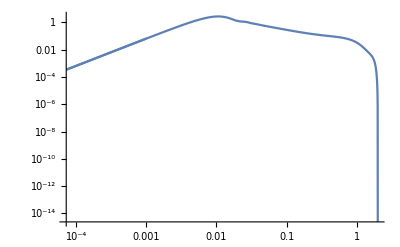

```mathematica
Show[LogLogPlot[{OMGWwb32[k,b,ksrh]},{k,k2,2},PlotRange->All],LogLogPlot[{OMGWwbshe[k,b,ksrh]},{k,10^(-3),k2},PlotRange->All]]
```

```mathematica
rangekk1=10^Range[-5,Log10[k2],0.001];rangekk2=10^Range[Log10[k2],Log10[2],0.001];
```

```mathematica
L1=Length[rangekk1];L2=Length[rangekk2];
```

```mathematica
OMGWb11=Table[{Log10[rangekk1[[i]]],Log10[f[0.01,rangekk1[[i]]]*OMGWwbshe[rangekk1[[i]],b,ksrh]]},{i,1,L1}];OMGWb12=Table[{Log10[rangekk2[[i]]],Log10[f[0.01,rangekk2[[i]]]*OMGWwb32[rangekk2[[i]],b,ksrh]]},{i,1,L2}];
```

```mathematica
rangekk=Join[rangekk1,rangekk2];
OMGWb1=Join[OMGWb11[[All,2]],OMGWb12[[All,2]]];
```

```mathematica
L=Length[rangekk];
```

```mathematica
OMGWb1list=Table[{Log10[rangekk[[i]]],OMGWb1[[i]]},{i,1,L}];
```

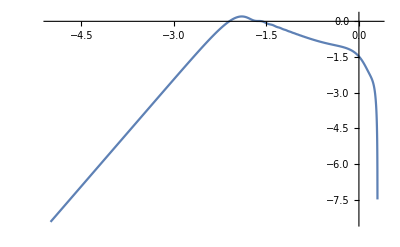

```mathematica
ListLinePlot[OMGWb1list]
```

```mathematica
Export["data/OMGWb32_001.dat",OMGWb1list];
```

```mathematica
L1=Length[rangekk1];L2=Length[rangekk2];
```

```mathematica
OMGWb11=Table[{Log10[rangekk1[[i]]],Log10[f[0.05,rangekk1[[i]]]*OMGWwbshe[rangekk1[[i]],b,ksrh]]},{i,1,L1}];OMGWb12=Table[{Log10[rangekk2[[i]]],Log10[f[0.05,rangekk2[[i]]]*OMGWwb32[rangekk2[[i]],b,ksrh]]},{i,1,L2}];
```

```mathematica
rangekk=Join[rangekk1,rangekk2];
OMGWb1=Join[OMGWb11[[All,2]],OMGWb12[[All,2]]];
```

```mathematica
L=Length[rangekk];
```

```mathematica
OMGWb1list=Table[{Log10[rangekk[[i]]],OMGWb1[[i]]},{i,1,L}];
```

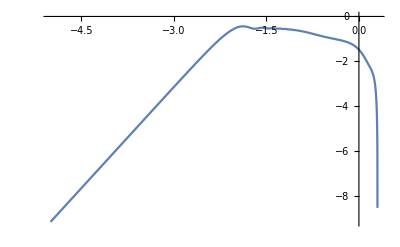

```mathematica
ListLinePlot[OMGWb1list]
```

```mathematica
Export["data/OMGWb32_005.dat",OMGWb1list];
```

## Plots 3

```mathematica
ksrh=10^2;b=2;k1=1/ksrh/(1+b);
ymax=Log10[OMGWwb2[1/ksrh,b,ksrh]]//N;
ymin=Log10[OMGWwbsh[k1,b,ksrh]]//N;
slope=A/.Flatten[Solve[{ymax==A*Log10[1/ksrh]+B,ymin==A*Log10[k1]+B},{A,B}]];
cnt=B/.Flatten[Solve[{ymax==A*Log10[1/ksrh]+B,ymin==A*Log10[k1]+B},{A,B}]];
```

```mathematica
OMGWwb2[k1,b,ksrh]/OMGWwbshe[k1,b,ksrh]//N
```

0.880331

```mathematica
DOMGWwb2[k_]=D[OMGWwb2[k,b,ksrh],k];
```

```mathematica
DOMGWwbshe[k_]=D[OMGWwbshe[k,b,ksrh],k];
```

```mathematica
k2=k/.FindRoot[DOMGWwb2[k]==DOMGWwbshe[k],{k,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.000025124

```mathematica
OMGWwb2[k2,b,ksrh]/OMGWwbshe[k2,b,ksrh]//N
```

1.

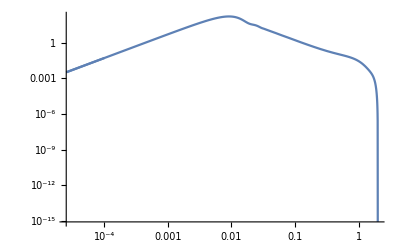

```mathematica
Show[LogLogPlot[{OMGWwb2[k,b,ksrh]},{k,k2,2},PlotRange->All],LogLogPlot[{OMGWwbshe[k,b,ksrh]},{k,10^(-4),k2},PlotRange->All]]
```

```mathematica
rangekk1=10^Range[-5,Log10[k2],0.001];rangekk2=10^Range[Log10[k2],Log10[2],0.001];
```

```mathematica
L1=Length[rangekk1];L2=Length[rangekk2];
```

```mathematica
OMGWb11=Table[{Log10[rangekk1[[i]]],Log10[f[0.01,rangekk1[[i]]]*OMGWwbshe[rangekk1[[i]],b,ksrh]]},{i,1,L1}];OMGWb12=Table[{Log10[rangekk2[[i]]],Log10[f[0.01,rangekk2[[i]]]*OMGWwb2[rangekk2[[i]],b,ksrh]]},{i,1,L2}];
```

```mathematica
rangekk=Join[rangekk1,rangekk2];
OMGWb1=Join[OMGWb11[[All,2]],OMGWb12[[All,2]]];
```

```mathematica
L=Length[rangekk];
```

```mathematica
OMGWb1list=Table[{Log10[rangekk[[i]]],OMGWb1[[i]]},{i,1,L}];
```

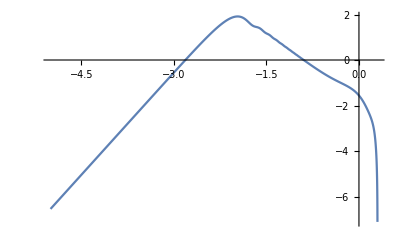

```mathematica
ListLinePlot[OMGWb1list]
```

```mathematica
Export["data/OMGWb2_001.dat",OMGWb1list];
```

```mathematica
L1=Length[rangekk1];L2=Length[rangekk2];
```

```mathematica
OMGWb11=Table[{Log10[rangekk1[[i]]],Log10[f[0.05,rangekk1[[i]]]*OMGWwbshe[rangekk1[[i]],b,ksrh]]},{i,1,L1}];OMGWb12=Table[{Log10[rangekk2[[i]]],Log10[f[0.05,rangekk2[[i]]]*OMGWwb2[rangekk2[[i]],b,ksrh]]},{i,1,L2}];
```

```mathematica
rangekk=Join[rangekk1,rangekk2];
OMGWb1=Join[OMGWb11[[All,2]],OMGWb12[[All,2]]];
```

```mathematica
L=Length[rangekk];
```

```mathematica
OMGWb1list=Table[{Log10[rangekk[[i]]],OMGWb1[[i]]},{i,1,L}];
```

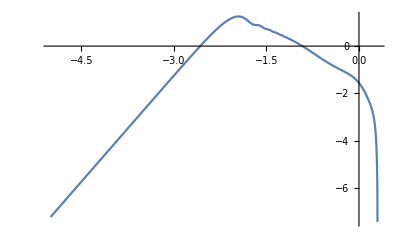

```mathematica
ListLinePlot[OMGWb1list]
```

```mathematica
Export["data/OMGWb2_005.dat",OMGWb1list];
```